Specialist Bee Only

```mathematica
NativePollen[n_]:= d*ϕ - (1/Ys)*((Us*n*s)/(1+Us*hs*n))
SpecialistBee[s_]:= (((Us*n*s)/(1+Us*hs*n)) - ms*s)
NativePlant[d_] := (r  (((s δ )/xreq)/(1+(s δ )/xreq)))*d*(1-d/Kd)
```

Solve for the equilibria

```mathematica
Solve[NativePollen[n] == 0, n]
```

{{n→(d Ys ϕ)/(Us (s-d hs Ys ϕ))}}

```mathematica
Solve[NativePollen[n]==0∧SpecialistBee[s]==0∧NativePlant[d]==0,{n, s, d}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{s→0,d→0},{n→-ms/((-1+hs ms) Us),s→0,d→0},{n→-ms/((-1+hs ms) Us),s→(Kd Ys ϕ)/ms,d→Kd}}

Run a simulation to see what is the fastest in reaching equilibrium values

{ϕ→300,Ys→0.25,Us→250,hs→1,ms→0.1,r→0.05,Kd→1000,xreq→10000,δ→2,n0→30000,s0→1,d0→100}

{{n→InterpolatingFunction[…],s→InterpolatingFunction[…],d→InterpolatingFunction[…]}}

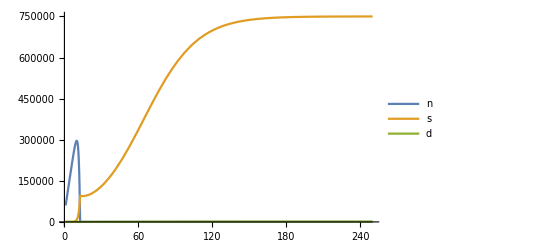

-Graphics-

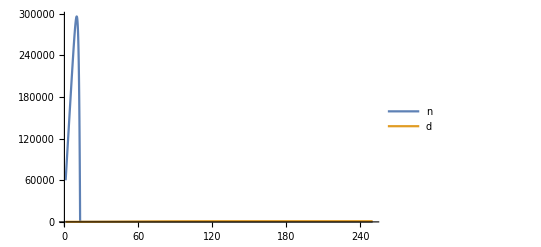

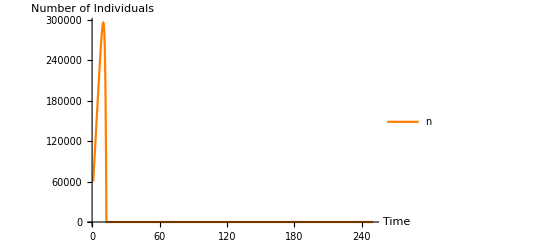

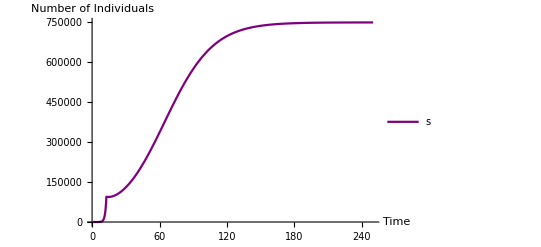

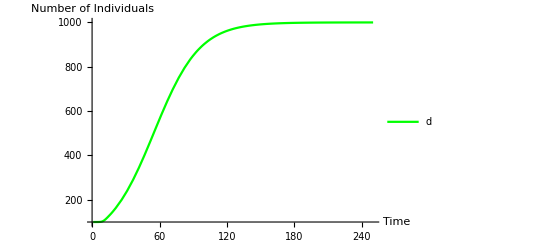

```mathematica
Clear[pars, δ, d, ϕ, Ys, hs,Us,ms,r,Kd,xreq,δ, n0,s0,d0]
pars = {ϕ -> 300, Ys -> 0.250, Us -> 250, hs ->1, ms -> 0.1, r -> 0.05, Kd -> 1000, xreq -> 10000, δ -> 2,n0 -> 30000, s0 -> 1, d0 -> 100}
tmax = 250;

sim[pars_]:= NDSolve[
{n'[t] ==d[t]*ϕ - (1/Ys)*((Us*n[t]*s[t])/(1+Us*hs*n[t])),
s'[t] == (s[t]((Us*n[t])/(1+Us*hs*n[t])) - ms*s[t]),
d'[t] == (r  (((s [t]δ )/xreq)/(1+(s[t] δ )/xreq)))*d[t]*(1-d[t]/Kd),
n[0]== n0,
s[0]==s0,
d[0]==d0}/. pars,
{n,s,d}, 
{t, 1, tmax}]
(*Set up the plot*)
sol = sim[pars]

Plot[{n[t]/.sol,s[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n, s,d}, PlotRange -> All]
Plot[{n[t]/.sol,s[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n, s,d}, PlotRange -> All]
Plot[{n[t]/.sol, d[t]/.sol}, {t, 1, tmax}, PlotLegends -> {n,d}, PlotRange -> All]
Plot[n[t]/.sol, {t, 1, tmax}, PlotLegends -> {n}, PlotRange -> All, PlotStyle -> {{Orange}}, AxesLabel->{"Time", "Number of Individuals"} ]
Plot[s[t]/.sol,{t, 1, tmax}, PlotLegends -> {s}, PlotRange -> All, PlotStyle -> {{Purple}}, AxesLabel->{"Time", "Number of Individuals"} ]
Plot[d[t]/.sol,{t, 1, tmax}, PlotLegends -> {d}, PlotRange -> All, PlotStyle -> {{Green}}, AxesLabel->{"Time", "Number of Individuals"} ]
```

It seems that the pollen reaches equilibrium exceptionally fast in this model, suggesting that we can use the Rapid Equilibrium Assumption for its dynamics on the system.

```mathematica
NativePollen[n_]:= d*ϕ - (1/Ys)*((Us*n*s)/(1+Us*hs*n))
SpecialistBee[s_]:= (((Us*n*s)/(1+Us*hs*n)) - ms*s)
NSolve[NativePollen[n] == 0, n]
Simplify[NSolve[(SpecialistBee[s]/.{n->(d Ys ϕ)/(Us (s-d hs Ys ϕ))}) == 0, s]]
```

{{n→(d Ys ϕ)/(Us (s-1. d hs Ys ϕ))}}

{{s→(d Ys ϕ)/ms}}

```mathematica
(((Us*n*s)/(1+Us*hs*n)) - ms*s) /. {n->(d Ys ϕ)/(Us (s-d hs Ys ϕ))}
```

-ms s+(d s Ys ϕ)/((s-d hs Ys ϕ) (1+(d hs Ys ϕ)/(s-d hs Ys ϕ)))

```mathematica
Clear[pars2, sol2]
```

```mathematica
pars2= {ϕ -> 300, Ys -> 0.250, hs -> 1, ms -> 0.1, r -> 0.05, Kd -> 1000, xreq -> 10000, δ -> 2, s0 -> 1, d0 -> 100}
```

{ϕ→300,Ys→0.25,hs→1,ms→0.1,r→0.05,Kd→1000,xreq→10000,δ→2,s0→1,d0→100}

{{s→InterpolatingFunction[…],d→InterpolatingFunction[…]}}

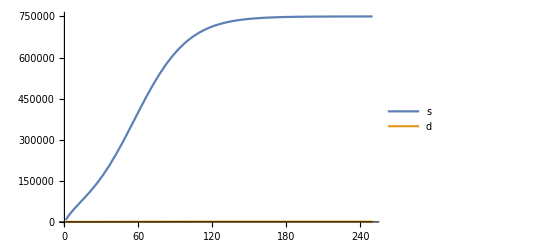

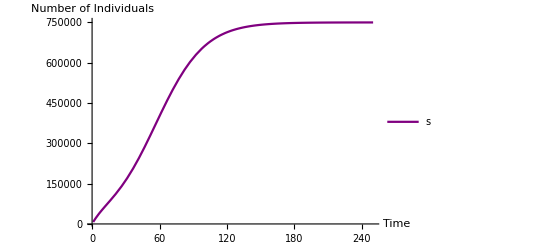

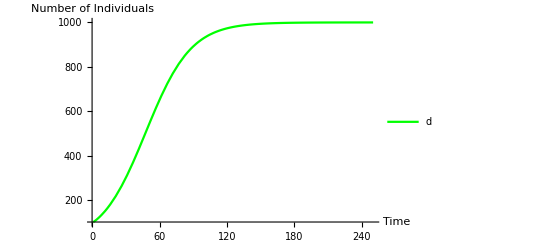

```mathematica
sim2[pars2_]:= NDSolve[
{
s'[t] ==( ((d[t] s[t] Ys ϕ)/((s[t]-d[t] hs Ys ϕ) (1+(d [t]hs Ys ϕ)/(s[t]-d[t] hs Ys ϕ))) )- ms*s[t]),
d'[t] == (r  (((s [t]δ )/xreq)/(1+(s[t] δ )/xreq)))*d[t]*(1-d[t]/Kd),
s[0]==s0,
d[0]==d0}/. pars2,
{s,d}, 
{t, 1, tmax}]
(*Set up the plot*)
sol2 = sim2[pars2]

Plot[{s[t]/.sol2, d[t]/.sol2}, {t, 1, tmax}, PlotLegends -> {s,d}, PlotRange -> All]
Plot[s[t]/.sol2,{t, 1, tmax}, PlotLegends -> {s}, PlotRange -> All, PlotStyle -> {{Purple}},AxesLabel->{"Time", "Number of Individuals"} ]
Plot[d[t]/.sol2,{t, 1, tmax}, PlotLegends -> {d}, PlotRange -> All, PlotStyle -> {{Green}}, AxesLabel->{"Time", "Number of Individuals"} ]
```

```mathematica
d[250] /. sim[pars]
d[250] /. sim2[pars2]
s[250] /. sim[pars]
s[250] /. sim2[pars2]
```

{999.938}

{999.957}

{749907.}

{749936.}